# Mosaic plots for data visualization

## Introduction

This notebook gives descriptions and examples of using the function MosaicPlot of the paclet "AntonAntonov/MosaicPlot".

The function MosaicPlot summarizes the conditional probabilities of co-occurrence of the categorical values in a list of records of the same length or a datasets. The list of records is assumed to be a full array and the columns to represent categorical values. (Note, that if a column is numerical, but has a small number of different values, then it can be seen as categorical.)

I have read the descriptions of mosaic plots in the book “R in Action” by Robert Kabakoff, [2], and one of the references provided in the book (“What is a mosaic plot?” by Steve Simon, [3]). I was impressed how informative mosaic plots are, and I figured they can be relatively easily implemented using Prefix trees (also known as “Tries”) [4,5].

Remark: The implementation of the paclet "AntonAntonov/MosaicPlot" is based on the paclet "AntonAntonov/TriesWithFrequences".

I implemented MosaicPlot while working on a document analyzing the census income data from 1998, [6]. This is the reason that dataset is used in this document. A good alternative dataset provided by WL is ExampleData[{“Statistics”,”USCars1993”}].

Remark: The original version of this document the WL / Mathematica package MosaicPlot.m provided by the project MathematicaForPrediction at GitHub, see [1].

Load the paclet

```mathematica
Needs["AntonAntonov`MosaicPlot`"]
```

Load the dataset

```mathematica
dsCensusData=ResourceFunction["ImportCSVToDataset"]["~/Downloads/adult/dfAdult.csv"]
```

## Data set

The data set can be found and taken from http://archive.ics.uci.edu/ml/datasets/Census+Income, [6].

The description of the data set is given in the file “adult.names” of the data folder. The data folder provides two sets with the same type of data “adult.data” and “adult.test”; the former is used for training, the latter for testing.

The total number of records in the file “adult.data” is 32561; the total number of records in the file “adult.test” is 16281.

Here is how the data looks like:

```mathematica
Magnify[RandomSample[dsCensusData,12],0.6]
```

Since I did not understand the meaning of the column “fnlwgt” I dropped it from the data:

```mathematica
dsCensusData=dsCensusData[All,KeyDrop[#,"fnlwgt"]&];
```

Here is the summary table of the data:

```mathematica
ResourceFunction["RecordsSummary"][dsCensusData[]]
```

{1 age
Min | 17.
1st Qu | 28.
Median | 37.
Mean | 38.5816
3rd Qu | 48.
Max | 90.,2 workclass
Private | 22696
Self-emp-not-inc | 2541
Local-gov | 2093
? | 1836
State-gov | 1298
Self-emp-inc | 1116
(Other) | 981,3 education
HS-grad | 10501
Some-college | 7291
Bachelors | 5355
Masters | 1723
Assoc-voc | 1382
11th | 1175
(Other) | 5134,4 education-num
Min | 1.
1st Qu | 9.
Median | 10.
Mean | 10.0807
3rd Qu | 12.
Max | 16.,5 marital-status
Married-civ-spouse | 14976
Never-married | 10683
Divorced | 4443
Separated | 1025
Widowed | 993
Married-spouse-absent | 418
Married-AF-spouse | 23,6 occupation
Prof-specialty | 4140
Craft-repair | 4099
Exec-managerial | 4066
Adm-clerical | 3770
Sales | 3650
Other-service | 3295
(Other) | 9541,7 relationship
Husband | 13193
Not-in-family | 8305
Own-child | 5068
Unmarried | 3446
Wife | 1568
Other-relative | 981,8 race
White | 27816
Black | 3124
Asian-Pac-Islander | 1039
Amer-Indian-Eskimo | 311
Other | 271,9 sex
Male | 21790
Female | 10771,10 capital-gain
1st Qu | 0.
3rd Qu | 0.
Median | 0.
Min | 0.
Mean | 1077.65
Max | 99999.,11 capital-loss
1st Qu | 0.
3rd Qu | 0.
Median | 0.
Min | 0.
Mean | 87.3038
Max | 4356.,12 hours-per-week
Min | 1.
1st Qu | 40.
Median | 40.
Mean | 40.4375
3rd Qu | 45.
Max | 99.,13 native-country
United-States | 29170
Mexico | 643
? | 583
Philippines | 198
Germany | 137
Canada | 121
(Other) | 1709,14 income
<=50K | 24720
>50K | 7841}

On the summary table the numerical variables are described with min, max, and quartiles. The category variables are described with the tallies of their values. The tallies of values are ordered in decreasing order. The tallies of truncated values are summed under the value “(Other)”.

Note that:
-- only 24% of the labels are “>50K”;
-- 2/3 of the records are for males;
-- “capital-gain” and “capital-loss” are very skewed.

## Explanations

If we pick a categorical variable, say “sex”, we can visualize the frequencies of the appearance of the variable values with the following plot:

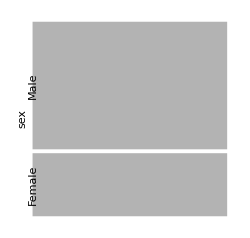

```mathematica
MosaicPlot[dsCensusData⟦All,{"sex"}⟧,ColorRules->{_->GrayLevel[0.7]},ImageSize->250]
```

The size of the rectangles depends on the frequencies of appearance of the values “Male” and “Female” in the data records. From the rectangle sizes we can see what we already knew from the data summary table: approximately 2/3 of the records are about males.

We can subdivide every rectangle r according to the frequencies of co-occurrence of r’s value with the values of a second categorical variable, say “relationship”:

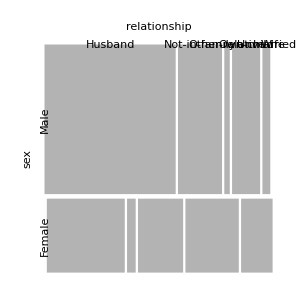

```mathematica
MosaicPlot[dsCensusData⟦All,{"sex","relationship"}⟧,"LabelRotation"->{{2,1.1},{0,1}},"ColumnNamesOffset"->0.075,ColorRules->{_->GrayLevel[0.7]},ImageSize->300]
```

The labels corresponding to the values of “relationship” are rotated for legibility. The "relationship" labels are placed according to the co-occurrence with the value "Male" of the variable "sex". The correspondent fractions of the pairs ("Female","Husband"), ("Female","Not-in-family"), etc., are deduced from the order of the "relationship" labels.

Using colored mosaic plots can help distinguishing which rectangles correspond to which values. Here is the last plot with rectangles colored across the "relationship" data variable:

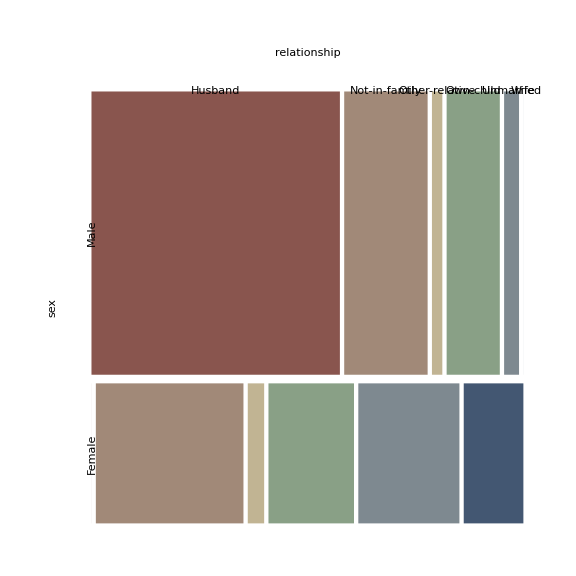

```mathematica
MosaicPlot[dsCensusData⟦All,{"sex","relationship"}⟧,"LabelRotation"->{{2,1.1},{0,1}},"ColumnNamesOffset"->0.09,ColorRules->Automatic,ImageSize->Large]
```

From the visual representations of the “sex vs. relationship” mosaic plot we can see that large fraction of the males are husbands, none (or a very small fraction) of them are wives. We can also see that none (or a very small fraction) of the females are husbands, the largest fraction of them are “Not-in-family”, and the “Not-in-family” females are approximately three times more than the females that are wives.

Let us make another mosaic plot for a different kind of relationship, “sex vs. education”:

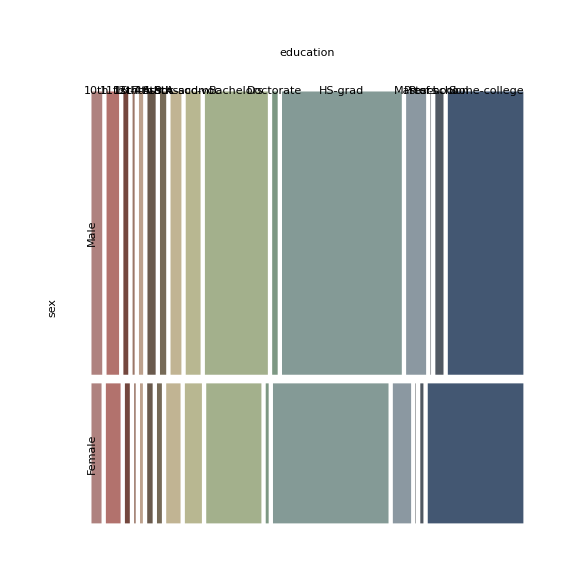

```mathematica
MosaicPlot[dsCensusData⟦All,{"sex","education"}⟧,"LabelRotation"->{{2,1.1},{0,1}},"ColumnNamesOffset"->0.09,ImageSize->Large]
```

By comparing the sizes of the rectangles corresponding to the values “Bachelors”, “Doctorate”, “Masters”, and “Some-college” on the “sex vs. education” mosaic plot we can see that the fraction of men that have finished college is larger than the fraction of women that have finished college.

We can further subdivide the rectangles according the co-occurrence frequencies with a third categorical variable. We are going to choose that third variable to be “income”, the values of which can be seen as outcomes or consequents of the values of the first two variables of the mosaic plot.

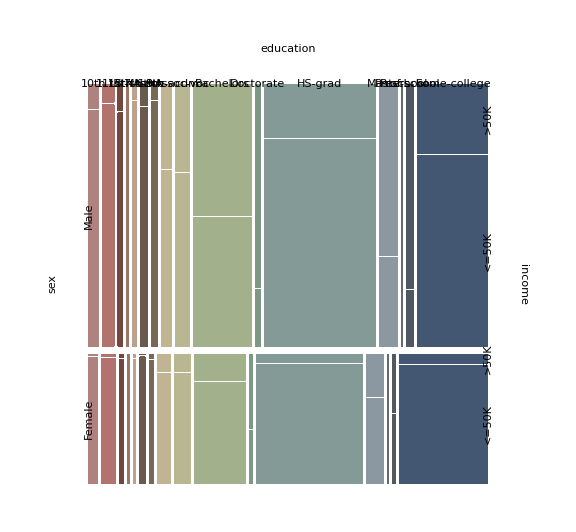

```mathematica
MosaicPlot[dsCensusData⟦All,{"sex","education","income"}⟧,"LabelRotation"->{{2,1.1},{0,1}},"ColumnNamesOffset"->0.09,ImageSize->Large]
```

From the mosaic plot “sex vs. education vs. income” we can make the following observations.
1. Approximately 75% of the males with doctorate degrees or with a professional school degree earn more than $50000 per year.
2. Approximately 60% of the females with a doctorate degree earn more than $50000 per year.
3. Approximately 45% of the females with a professional school degree earn more than $50000.
4. Across all education type females are (much) less likely to earn more than $50000 per year.

(The exact numbers of these observations can be seen tooltip table shown when hovering with the mouse over the rectangles.)

Instead of having the consequent (or outcome) variable to be the last variable in the mosaic plot, it is also useful to start with the consequent variable to get a perspective of how the attributes breakdown for it. Here is an example of a mosaic plot for “income vs. relationship vs. sex” (using a different color scheme):

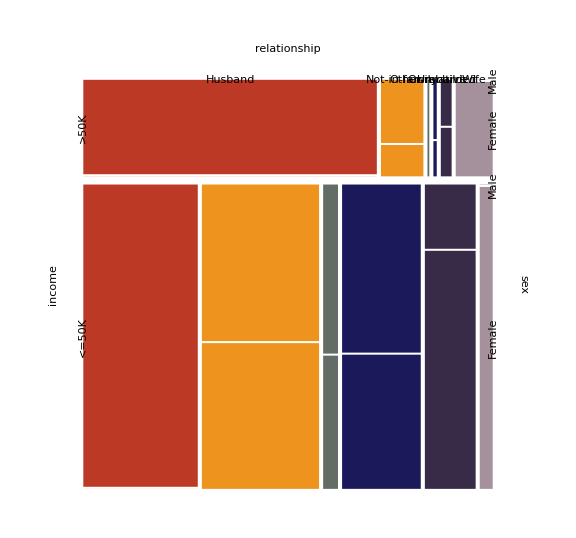

```mathematica
MosaicPlot[dsCensusData[All,{"income","relationship","sex"}],"LabelRotation"->{{2,1.1},{0,1}},"ColumnNamesOffset"->0.075,ColorRules->{2->ColorData[9,"ColorList"]},ImageSize->Large]
```

From the mosaic plot “income vs. relationship vs. sex” we can see that 75% of the people with income higher than $50000 are male and husbands. We can also see that large fraction, 30%, of the people with income less than $50000 are “Not-in-family” and they are equally likely to be male or female. People who are not in a family are only 10% of the people with income higher than $50000.

It might be useful to make a mosaic plot for a subset of the records. Here is an example of a mosaic plot with splitting across four columns made only for people who have bachelor, master, or doctorate degrees:

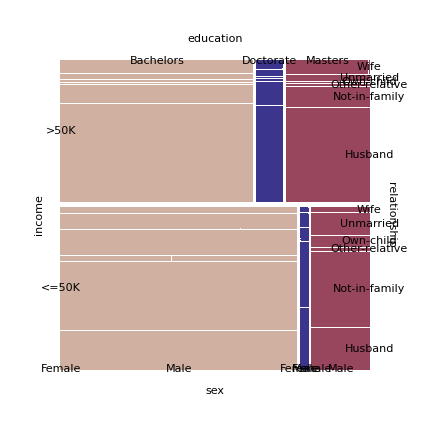

```mathematica
Block[{dsCensusData=dsCensusData[Select[MemberQ[{"Bachelors","Masters","Doctorate"},#education]&]]},
MosaicPlot[dsCensusData⟦All,{"income","education","relationship","sex"}⟧,"Gap"->0.02,"GapFactor"->0.56,"ColumnNamesOffset"->0.07,"LabelRotation"->{{3,1},{1,1}},ColorRules->{2->ColorData[13,"ColorList"]},ImageSize->430]]
```

Similar to the previous mosaic plot is this plot of “sex vs. education vs. marital-status vs. income”:

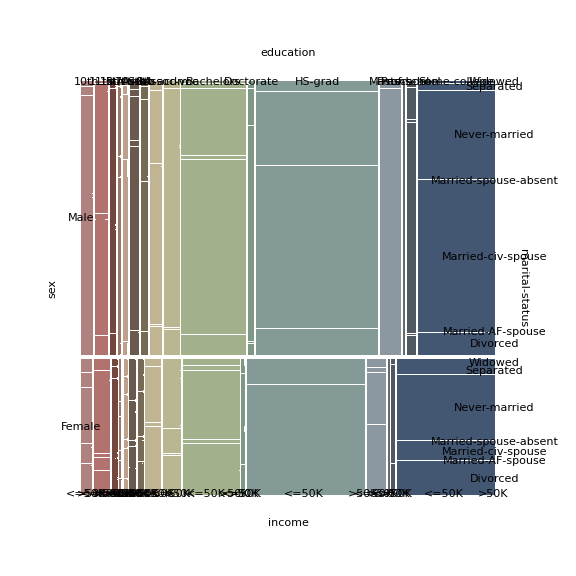

```mathematica
MosaicPlot[dsCensusData⟦All,{"sex","education","marital-status","income"}⟧,"Gap"->0.012,"GapFactor"->0.56,"ColumnNamesOffset"->0.07,"LabelRotation"->{{3,1},{1,1}},ImageSize->Large]
```

## Options

MosaicPlot takes the following options:

```mathematica
ColumnForm[Complement[Options[MosaicPlot],Options[Graphics]]]
AutoCollapse[]
```

ColumnNames→None
ColumnNamesOffset→0.05
ExpandLastColumn→False
FirstAxis→y
Gap→0.02
GapFactor→0.5
LabelRotation→{{1,0},{0,1}}
LabelStyle→{}
Tooltips→True
ZeroProbability→0.001
ColorRules→Automatic

{Null}

In addition, MosaicPlot takes all the options of Graphics. (Because MosaicPlot is implemented with Graphics.)

The options are explained in the sub-sections below.

### Visualizing categorical columns + a numerical column (“ExpandLastColumn”)

If the last data column is numerical then MosaicPlot can use it as pre-computed contingency statistics. This functionality is specified with the option “ExpandLastColumn”→True.

In order to explain the functionality we are going to use following interpretation. If the last of column of the data is numerical then we can treat the data as a contracted version of a longer list of records made only of the categorical columns. For example, consider the following table with observations of people’s hair and eyes color:

```mathematica
dsRand={{"blond","blue",3},{"blond","brown",1},{"dark","blue",1},{"dark","brown",4}};
Magnify[TableForm[dsRand,TableHeadings->{None,Map[Style[#,FontFamily->"Times"]&,{"hair color","eyes color","number of observations"}]}],1]
```

hair color | eyes color | number of observations
blond | blue | 3
blond | brown | 1
dark | blue | 1
dark | brown | 4

The table above can be considered as a contracted version of this table:

```mathematica
Magnify[TableForm[Flatten[Table[Most[#],{Last[#]}]&/@dsRand,1],TableHeadings->{None,Map[Style[#,FontFamily->"Times"]&,{"hair color","eyes color"}]}],1]
```

hair color | eyes color
blond | blue
blond | blue
blond | blue
blond | brown
dark | blue
dark | brown
dark | brown
dark | brown
dark | brown

Setting the option “ExpandLastColumn” to True gives a mosaic plot corresponding to that latter, observations-expanded table:

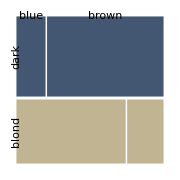

```mathematica
MosaicPlot[dsRand,"ExpandLastColumn"->True,ImageSize->Small]
```

The last data column (which is numerical) does not need to be made of integers:

```mathematica
dsRand⟦All,3⟧=dsRand⟦All,3⟧/20.;
dsRand
```

{{blond,blue,0.15},{blond,brown,0.05},{dark,blue,0.05},{dark,brown,0.2}}

```mathematica
MosaicPlot[dsRand,"ExpandLastColumn"->True,ImageSize->Small]
```

-Graphics-

### Controlling the size of the gap between the rectangles (“Gap” and “GapFactor”)

The size of the gaps between the rectangles is controlled with the options “Gap” and “GapFactor”. The value “Gap” specifies the size of the gap between the rectangles derived from the first column. MosaicPlot splits the data into rectangles recursively. In order to derive the gaps for the subsequent data column the values of “Gap” and “GapFactor” are multiplied. In other words, if MosaicPlot is given the options {“Gap”→g,“GapFactor”→f} then the gap between the rectangles corresponding to the i-th column have the size is g f^(i-1).

### Contingency values labels (“LabelRotation” and “LabelStyle”)

The labels derived from the distinct values (levels) of each column of the data can be rotated and given style options.

The option “LabelRotation” takes directional specification for Text (the fourth argument of Text). The option “LabelStyle” takes options and arguments for the function Style.

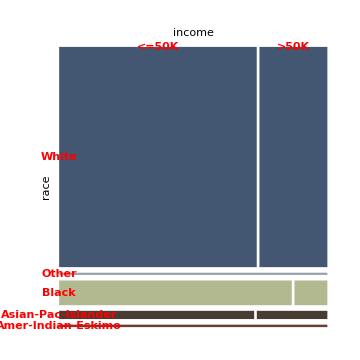

```mathematica
MosaicPlot[dsCensusData⟦All,{8,14}⟧,"LabelRotation"->{{1,0},{1,1}},"LabelStyle"->{Bold,Red,FontFamily->"Times"},ImageSize->Medium]
```

### Labels for categorical variables (“ColumnNames” and “ColumnNamesOffset”)

The names of the data columns (data’s variables) are specified with the option “ColumnNames”. (The list of names given to “ColumnNames” can be formatted with Style.) The distance of the column names from the rectangles is specified with the option “ColumnNamesOffset”.

### Start of the rectangle splitting (“FirstAxis”)

The starting axis of the data splitting is specified by “FirstAxis”.

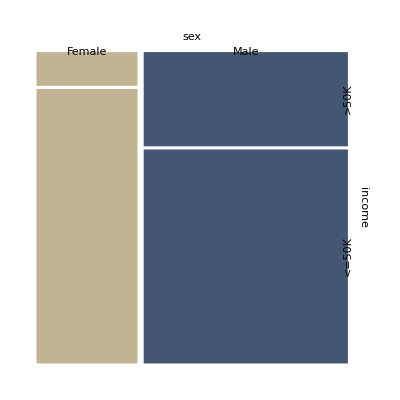
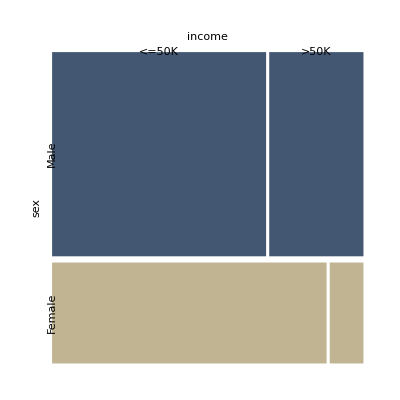

```mathematica
MosaicPlot[dsCensusData⟦All,{9,14}⟧,"FirstAxis"->#]&/@{"x","y"}
```

### Tooltips with exact contingency statistics (“Tooltips”)

MosaicPlot has an interactive feature using Tooltip that gives a table with the exact co-occurrence (contingency) values when hovering with the mouse over the rectangles. The option “Tooltips” takes the values True or False.

### Visualizing non-existing contingencies (“ZeroProbability”)

The non-existing contingencies have to be represented in the mosaic plot. MosaicPlot uses very thin rectangles for them and the size of these rectangles is controlled with the option “ZeroProbability”.

### Coloring of the rectangles (ColorRules)

The rectangles can be colored using the option ColorRules which specifies how the colors of the rectangles are determined from the indices of the data columns.

More precisely, the values of the option ColorRules should be a list of rules, {i_1→c_1,i_2→c_2,...}, matching the form

{(_Integer→(_RGBColor|_GrayLevel))..}.

The column indices i_k can be negative (-1 meaning the last column).

If coloring for only one column index is specified the value of ColorRules can be of the form

{_Integer→{(_RGBColor|_GrayLevel)..}}.

The colors are used with Blend in order to color the rectangles according to the order of the unique values of the specified data columns.

The grid of plots below shows mosaic plots of the same data with different values for the option ColorRules (given as plot labels).

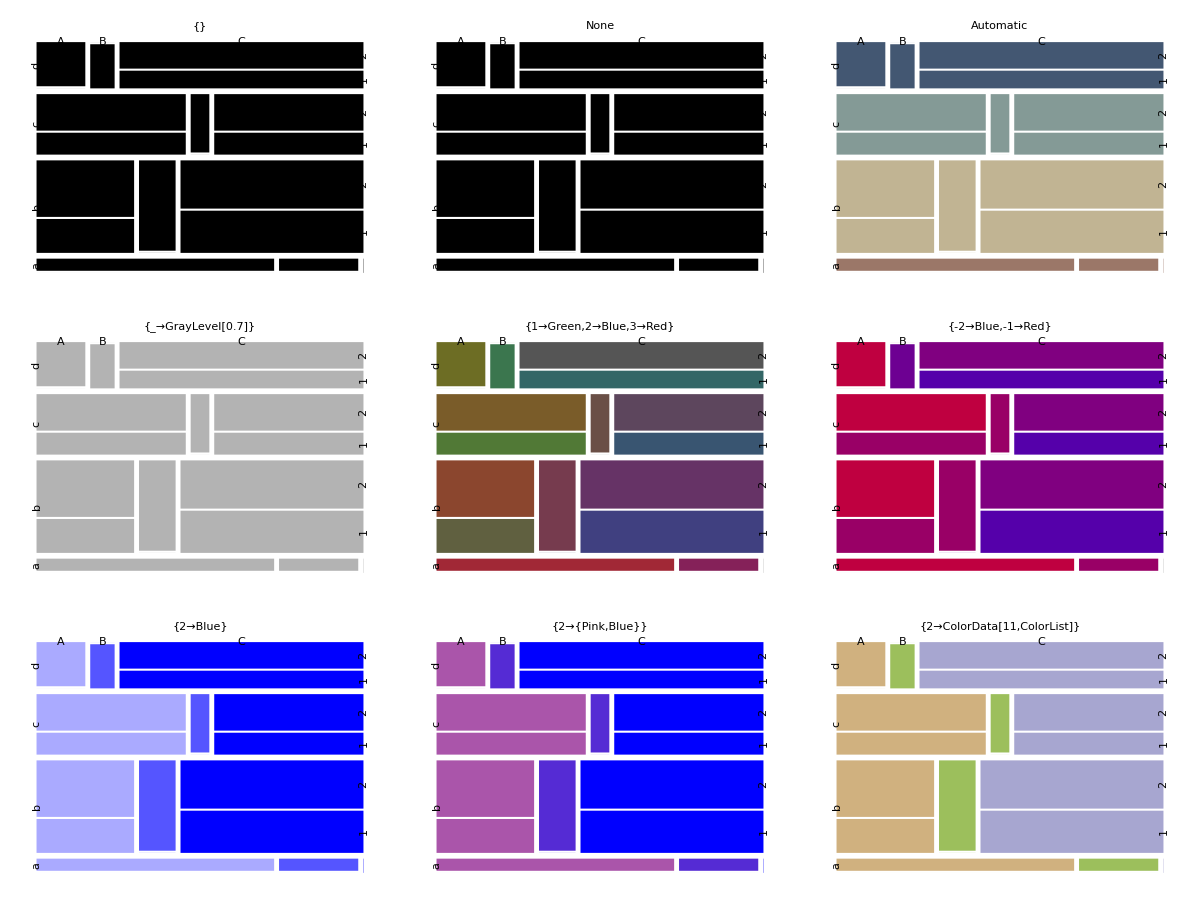

```mathematica
lsRand=Table[{RandomChoice[{1,4,5,2}->{"a","b","c","d"}],RandomChoice[{4,1,5}->{"A","B","C"}],RandomChoice[{1,2}->{"1","2"}]},{60}];
t=MosaicPlot[lsRand,PlotLabel->If[TrueQ[#===None],"None",#],ColorRules->ReleaseHold[#],"Gap"->0.025,"GapFactor"->0.6,ImageSize->200]&/@{{},None,Automatic,{_->GrayLevel[0.7]},HoldForm[{1->Green,2->Blue,3->Red}],HoldForm[{-2->Blue,-1->Red}],HoldForm[{2->Blue}],HoldForm[{2->{Pink,Blue}}],HoldForm[{2->ColorData[11,"ColorList"]}]};
Grid[ArrayReshape[t,{3,3},""],Dividers->All]
```

The default value for ColorRules is Automatic. When Automatic is given to ColorRules, MosaicPlot finds the data column with the largest number of unique values and colors them according to their order using ColorData[7,”ColorList”].

## References

[1] Anton Antonov, Mosaic plot for data visualization implementation in Mathematica, source code at GitHub, https://github.com/antononcube/MathematicaForPrediction, package MosaicPlot.m, (2013).

[2] Robert Kabacoff, R in Action, Manning Publications, 1 edition, 2011, URL: http://www.amazon.com/R-Action-Robert-Kabacoff/dp/1935182390 .

[3] Steve Simon, What is a mosaic plot?, URL: http://www.pmean.com/definitions/mosaic.htm .

[4] Anton Antonov, Tries with frequencies Mathematica package, source code at GitHub, https://github.com/antononcube/MathematicaForPrediction, package TriesWithFrequencies.m, (2013).

[5] Wikipedia, Trie, http://en.wikipedia.org/wiki/Trie .

[6] Ronny Kohavi and Barry Becker  (1996), Census Income Data Set, at UCI Machine Learning Repository. URL: http://archive.ics.uci.edu/ml/datasets/Census+Income .

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

AntonAntonov/MosaicPlot

AntonAntonov`MosaicPlot`

AntonAntonov/MosaicPlot/tutorial/Mosaicplotsfordatavisualization

### Keywords